### Basic Examples (7)

A sphere:

```mathematica
sphere[a_][u_,v_]:={a Cos[v] Cos[u],a Cos[v] Sin[u],a Sin[v]}
```

Equations for geodesics on a sphere:

```mathematica
ge=[sphere[1][u,v],{u,v},t,{0,0},θ]
```

{-2 Tan[v[t]] u'[t] v'[t]+u''[t]==0,Cos[v[t]] Sin[v[t]] u'[t]^2+v''[t]==0,u[0]==0,v[0]==0,u'[0]==Cos[θ],v'[0]==Sin[θ]}

A set of numerical solutions of equations for geodesics of a sphere:

```mathematica
sg=Flatten[(NDSolve[#1,{u,v},{t,0,4}]&)/@Table[ge,{θ,(2 π)/30,2 π,(2 π)/30}],1];
```

Evaluate the geodesic at a definite point:

```mathematica
sphere[1][u[t],v[t]]/.sg[[1]]/.t->.1
```

{0.995004,0.0976518,0.0207565}

Plot solutions in a plane:

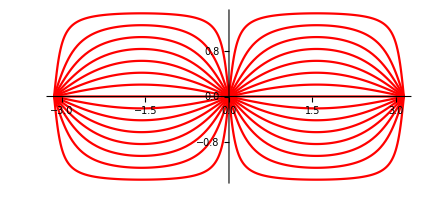

```mathematica
ParametricPlot[Evaluate[{u[t],v[t]}/.sg], {t,0,π},
      PlotRange->All, PlotStyle->Hue[0]]
```

Plot geodesics on a sphere:

```mathematica
ParametricPlot3D[Evaluate[sphere[1][u[t],v[t]]/.sg], {t,0,π}]
```

-Graphics3D-

Plot the geodesic circles (locus surface points located at a given geodesic radius):

```mathematica
Graphics3D[Table[Line[Append[#,First[#]]&[sphere[1][u[t],v[t]]/.sg]],{t,0,3,1/5}]]
```

-Graphics3D-

### Scope (3)

A torus:

```mathematica
torus[a_,b_,c_][u_,v_]:={(a+b Cos[v]) Cos[u],(a+b Cos[v]) Sin[u],c Sin[v]}
```

The equations for geodesics:

```mathematica
[torus[3,1,1][u,v],{u,v},t,{2,3},θ]
```

{-((2 Sin[v[t]] u'[t] v'[t])/(3+Cos[v[t]]))+u''[t]==0,(3+Cos[v[t]]) Sin[v[t]] u'[t]^2+v''[t]==0,u[0]==2,v[0]==3,u'[0]==Cos[θ],v'[0]==Sin[θ]}

Solve a geodesic for large t:

```mathematica
Show[ParametricPlot3D[Evaluate[torus[3,1,1][u[t],v[t]]/.NDSolve[[torus[3,1,1][u,v],{u,v},t,{π,π},.5],{u,v},{t,0,150}]],{t,0,150},Boxed->False,Axes->False],ParametricPlot3D[Evaluate[torus[3,1,1][u,v]],{u,0,2π},{v,0,2π},PlotStyle->Opacity[.5],Mesh->False]]
```

-Graphics3D-

Solve for geodesics:

```mathematica
sg=Flatten[Table[NDSolve[[torus[3,1,1][u,v],{u,v},t,{π,π},θ],{u,v},{t,0,4π}], {θ, 2π/30, 2π, 2π/30}], 1];
```

Plot solutions in a plane:

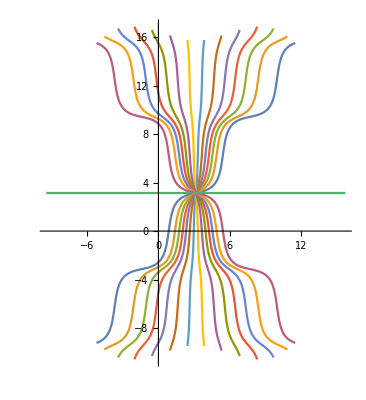

```mathematica
ParametricPlot[Evaluate[{u[s],v[s]}/.sg],{s,0,4π}]
```

Solve for a set of geodesics:

```mathematica
Show[ParametricPlot3D[Evaluate[torus[3,1,1][u,v]],{u,0,3π/2},{v,π,2π},PlotStyle->Opacity[.5],Mesh->False,Boxed->False,Axes->False],ParametricPlot3D[Evaluate[torus[3,1,1][u[t],v[t]]/.sg],{t,0,4π}]]
```

-Graphics-

Plot the geodesic circles:

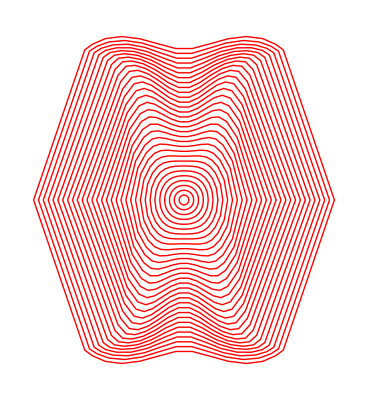

```mathematica
Show[Graphics[{Red,Table[Line[Append[#,First[#]]&[{u[t],v[t]}/.sg]],
    {t,0,2π,1/5}]}]]
```

Plot the geodesic circles over the torus:

```mathematica
sg=Flatten[Table[NDSolve[[torus[3,1,1][u,v],{u,v},t,{π,π},θ],{u,v},{t,0,2.5}], {θ, 2π/200, 2π, 2π/200}], 1];
```

```mathematica
ta= Table[Line[Append[#,First[#]]&[torus[3,1,1][u[t],v[t]]/.sg]], {t,0,2.5,.5}];
Show[Graphics3D[{Thickness[.005], Hue[.7],ta}],ParametricPlot3D[Evaluate[torus[3,1,1][u,v]],{u,0,2π},{v,0,2π},PlotStyle->Opacity[.5],Mesh->False,Boxed->False,Axes->False], Boxed->False]
```

-Graphics3D-

Define a monkey saddle:

```mathematica
ms=Entity["Surface","MonkeySaddle"]["ParametricEquations"][1][u,v]
```

{u,v,u^3-3 u v^2}

Get the equations for geodesics:

```mathematica
ge=[ms,{u,v},t,{0,0},θ]//FullSimplify
```

{(18 (u[t]^2-v[t]^2) (-2 v[t] u'[t] v'[t]+u[t] (u'[t]^2-v'[t]^2)))/(1+9 (u[t]^2+v[t]^2)^2)+u''[t]==0,(36 u[t] v[t] (2 v[t] u'[t] v'[t]+u[t] (-u'[t]^2+v'[t]^2)))/(1+9 (u[t]^2+v[t]^2)^2)+v''[t]==0,u[0]==0,v[0]==0,Cos[θ]==u'[0],Sin[θ]==v'[0]}

Solve the equations for geodesics:

```mathematica
sd=With[{u0=0,v0=0,a=0,n=100,tf=2},Flatten[((NDSolve[#1,{u,v},{t,0,2}])&)/@Table[ge,{θ,(2 π)/n,2 π,(2 π)/n}],1]];
```

Plot solutions for geodesics:

```mathematica
ParametricPlot[Evaluate[{u[t],v[t]}/.sd],{t,0,2}]
```

-Graphics-

Plot the geodesics over the surface:

```mathematica
Show[ParametricPlot3D[Evaluate[ms],{u,-2,2},{v,-π,π},PlotRange->1.5,PlotStyle->Opacity[.5],Mesh->False],ParametricPlot3D[Evaluate[ms/.{u->u[t],v->v[t]}/.sd],{t,0,2}]]
```

-Graphics-

Plot the geodesic circles:

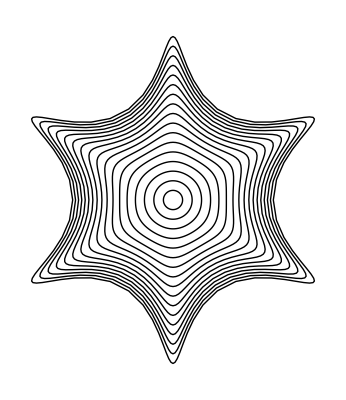

```mathematica
Graphics[Table[Line[Append[{u[t],v[t]}/.sd,{u[t],v[t]}/.sd[[1]]]],{t,0,1.7,.1}]]
```

Plot the geodesics circles over the surface:

```mathematica
Show[ParametricPlot3D[Evaluate[ms],{u,-2,2},{v,-π,π},PlotRange->1.5,PlotStyle->Opacity[.5],Mesh->False],Graphics3D[Table[Line[Append[ms/.{u->u[t],v->v[t]}/.sd,ms/.{u->u[t],v->v[t]}/.sd[[1]]]],{t,0,1.7,.1}]]]
```

-Graphics3D-

A pseudosphere:

```mathematica
pseudosphere[a_][u_,v_]:= 
   a{Cos[u]Sin[v], Sin[u]Sin[v], Cos[v]+Log[.001+Tan[v/2]]}
```

The geodesic equations:

```mathematica
P= {5.3,2.5};
```

```mathematica
[pseudosphere[1][u,v],{u,v},t,P,θ];
```

Plot the geodesic equations in 3D varying θ:

```mathematica
plot=Show[ParametricPlot3D[.99 pseudosphere[1][u,v],{u,0,2 π},{v,0,π-.01},Mesh->None,PlotStyle->Opacity[.5]],Graphics3D[{PointSize[.03],Point[pseudosphere[1]@@P]}]];
```

```mathematica
Manipulate[Show[ParametricPlot3D[Evaluate[pseudosphere[1][u[t],v[t]]/.NDSolve[[pseudosphere[1][u,v],{u,v},t,P,θ],{u,v},{t,0,10}]],{t,0,10},PlotRange->{{-1,1},{-1,1},{0,3.5}}],plot],{{θ,1.3},0,π}]
```

-Graphics-

A top view of a solution:

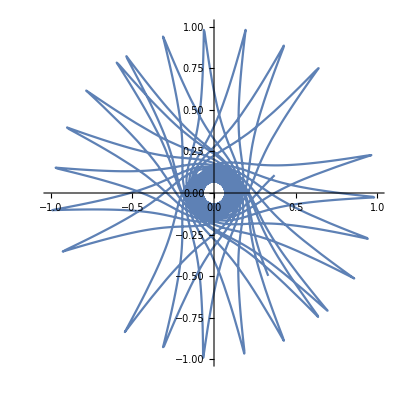

```mathematica
Module[{θ=1.3},ParametricPlot[Evaluate[Most[First[pseudosphere[1][u[t],v[t]]/.NDSolve[[pseudosphere[1][u,v],{u,v},t,P,θ],{u,v},{t,0,120}]]]],{t,0,120},PlotRange->1]]
```